#### Comet Strong Scale Plot

```mathematica
file="/Users/WillC/Documents/Rutgers/Research/RADICAL/Cloud-Master/data/output/Comet_test_002/strong_scale_output/data.csv";
rawdata= Import[file];
rawdata[[;;,;;1]]
rawdata=Table[{rawdata[[x]][[3]],rawdata[[x]][[2]],rawdata[[x]][[4]]},{x,1,Length[rawdata]}];
header = rawdata[[1]]
data = rawdata[[2;;,;;]]
```

{{Test Directory},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output000},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output001},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output002},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output003},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output004},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output005},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output006},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output007},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output008},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output009},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output010},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output011},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output012},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output013},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output014},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output015},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output016},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output017},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output018},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output019},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output020},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output021},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output022},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output023},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output024},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output025},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output026},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output027},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output028},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output029},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output030},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output031},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output032},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output033},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output034},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output035},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output036},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output037},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output038},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output039},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output040},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output041},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output042},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output043},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output044},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output045},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output046},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output047},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output048},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output049},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output050},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output051},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output052},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output053},{/home/willc97/Cloud-Master/data/output/Comet_test_002/strong_scale_output/single_run_output054}}

{2 ^ Number of Cores,2 ^ Number of Jobs,Run Time}

{{1.,1.,4.35214},{2.,1.,4.24437},{4.,1.,4.3205},{8.,1.,4.32166},{16.,1.,4.24557},{1.,2.,7.75619},{2.,2.,4.35357},{4.,2.,4.31797},{8.,2.,4.35321},{16.,2.,4.36246},{1.,4.,14.466},{2.,4.,7.77794},{4.,4.,4.99676},{8.,4.,4.38764},{16.,4.,4.27349},{1.,8.,29.2647},{2.,8.,14.5691},{4.,8.,9.04696},{8.,8.,4.36745},{16.,8.,4.37741},{1.,16.,55.5054},{2.,16.,28.3908},{4.,16.,14.5461},{8.,16.,7.75452},{16.,16.,4.24289},{1.,32.,107.987},{2.,32.,56.2207},{4.,32.,28.9703},{8.,32.,14.6757},{16.,32.,8.46133},{1.,64.,220.179},{2.,64.,110.914},{4.,64.,56.9265},{8.,64.,29.2017},{16.,64.,14.6901},{1.,128.,435.014},{2.,128.,223.313},{4.,128.,111.028},{8.,128.,56.6231},{16.,128.,28.596},{1.,256.,874.525},{2.,256.,449.248},{4.,256.,219.697},{8.,256.,112.968},{16.,256.,56.6998},{1.,512.,1736.91},{2.,512.,899.295},{4.,512.,443.147},{8.,512.,219.808},{16.,512.,111.567},{1.,1024.,3482.41},{2.,1024.,1773.7},{4.,1024.,888.504},{8.,1024.,447.929},{16.,1024.,223.907}}

```mathematica
testsPerNumCores=5;
sleepTime=3;
precision=4;
strongScale=Table[data[[testsPerNumCores*x+y]],{y,1,11},{x,0,4}]
strongScaleCores=Table[
IntegerPart[strongScale[[x]][[y]][[1]]]
,{x,1,Length[strongScale]}
,{y,1,Length[strongScale[[1]]]}
];
strongScaleJobs=Table[ToString[IntegerPart[strongScale[[x]][[y]][[2]]]],{x,1,Length[strongScale]},{y,1,Length[strongScale[[x]]]}];
strongScaleExperimental=Table[strongScale[[x]][[y]][[3]],{x,1,Length[strongScale]},{y,1,Length[strongScale[[x]]]}]
strongScaleExpected=Table[3*strongScale[[x]][[y]][[2]]/strongScale[[x]][[y]][[1]],{x,1,Length[strongScale]},{y,1,Length[strongScale[[x]]]}];
strongScaleOverhead=strongScaleExperimental-strongScaleExpected

strongScaleCompare=Table[{strongScaleOverhead[[x]][[y]],strongScaleExperimental[[x]][[y]]},{x,1,Length[strongScale]},{y,1,Length[strongScale[[x]]]}]
```

{{{1.,1.,4.35214},{1.,2.,7.75619},{1.,4.,14.466},{1.,8.,29.2647},{1.,16.,55.5054}},{{2.,1.,4.24437},{2.,2.,4.35357},{2.,4.,7.77794},{2.,8.,14.5691},{2.,16.,28.3908}},{{4.,1.,4.3205},{4.,2.,4.31797},{4.,4.,4.99676},{4.,8.,9.04696},{4.,16.,14.5461}},{{8.,1.,4.32166},{8.,2.,4.35321},{8.,4.,4.38764},{8.,8.,4.36745},{8.,16.,7.75452}},{{16.,1.,4.24557},{16.,2.,4.36246},{16.,4.,4.27349},{16.,8.,4.37741},{16.,16.,4.24289}},{{1.,2.,7.75619},{1.,4.,14.466},{1.,8.,29.2647},{1.,16.,55.5054},{1.,32.,107.987}},{{2.,2.,4.35357},{2.,4.,7.77794},{2.,8.,14.5691},{2.,16.,28.3908},{2.,32.,56.2207}},{{4.,2.,4.31797},{4.,4.,4.99676},{4.,8.,9.04696},{4.,16.,14.5461},{4.,32.,28.9703}},{{8.,2.,4.35321},{8.,4.,4.38764},{8.,8.,4.36745},{8.,16.,7.75452},{8.,32.,14.6757}},{{16.,2.,4.36246},{16.,4.,4.27349},{16.,8.,4.37741},{16.,16.,4.24289},{16.,32.,8.46133}},{{1.,4.,14.466},{1.,8.,29.2647},{1.,16.,55.5054},{1.,32.,107.987},{1.,64.,220.179}}}

{{4.35214,7.75619,14.466,29.2647,55.5054},{4.24437,4.35357,7.77794,14.5691,28.3908},{4.3205,4.31797,4.99676,9.04696,14.5461},{4.32166,4.35321,4.38764,4.36745,7.75452},{4.24557,4.36246,4.27349,4.37741,4.24289},{7.75619,14.466,29.2647,55.5054,107.987},{4.35357,7.77794,14.5691,28.3908,56.2207},{4.31797,4.99676,9.04696,14.5461,28.9703},{4.35321,4.38764,4.36745,7.75452,14.6757},{4.36246,4.27349,4.37741,4.24289,8.46133},{14.466,29.2647,55.5054,107.987,220.179}}

{{1.35214,1.75619,2.46602,5.26468,7.50542},{2.74437,1.35357,1.77794,2.56909,4.39078},{3.5705,2.81797,1.99676,3.04696,2.54611},{3.94666,3.60321,2.88764,1.36745,1.75452},{4.05807,3.98746,3.52349,2.87741,1.24289},{1.75619,2.46602,5.26468,7.50542,11.9873},{1.35357,1.77794,2.56909,4.39078,8.22072},{2.81797,1.99676,3.04696,2.54611,4.9703},{3.60321,2.88764,1.36745,1.75452,2.67565},{3.98746,3.52349,2.87741,1.24289,2.46133},{2.46602,5.26468,7.50542,11.9873,28.179}}

{{{1.35214,4.35214},{1.75619,7.75619},{2.46602,14.466},{5.26468,29.2647},{7.50542,55.5054}},{{2.74437,4.24437},{1.35357,4.35357},{1.77794,7.77794},{2.56909,14.5691},{4.39078,28.3908}},{{3.5705,4.3205},{2.81797,4.31797},{1.99676,4.99676},{3.04696,9.04696},{2.54611,14.5461}},{{3.94666,4.32166},{3.60321,4.35321},{2.88764,4.38764},{1.36745,4.36745},{1.75452,7.75452}},{{4.05807,4.24557},{3.98746,4.36246},{3.52349,4.27349},{2.87741,4.37741},{1.24289,4.24289}},{{1.75619,7.75619},{2.46602,14.466},{5.26468,29.2647},{7.50542,55.5054},{11.9873,107.987}},{{1.35357,4.35357},{1.77794,7.77794},{2.56909,14.5691},{4.39078,28.3908},{8.22072,56.2207}},{{2.81797,4.31797},{1.99676,4.99676},{3.04696,9.04696},{2.54611,14.5461},{4.9703,28.9703}},{{3.60321,4.35321},{2.88764,4.38764},{1.36745,4.36745},{1.75452,7.75452},{2.67565,14.6757}},{{3.98746,4.36246},{3.52349,4.27349},{2.87741,4.37741},{1.24289,4.24289},{2.46133,8.46133}},{{2.46602,14.466},{5.26468,29.2647},{7.50542,55.5054},{11.9873,107.987},{28.179,220.179}}}

#### Comet Weak Scale Plot

```mathematica
file="/Users/WillC/Documents/Rutgers/Research/RADICAL/Cloud-Master/data/output/Comet_test_001/weak_scale_output/data.csv";
rawdata= Import[file];
header = rawdata[[1,2;;]]
data = rawdata[[2;;,2;;]]
```

{2 ^ Number of Cores,2 ^ Jobs per Cores,Run Time}

{{1.,1.,4.33969},{1.,2.,7.74974},{1.,4.,14.5627},{1.,8.,27.7742},{1.,16.,58.1951},{1.,32.,112.432},{1.,64.,215.876},{1.,128.,434.515},{1.,256.,869.557},{1.,512.,1752.21},{1.,1024.,3455.97},{2.,1.,4.44316},{2.,2.,7.95156},{2.,4.,14.9646},{2.,8.,28.957},{2.,16.,55.5302},{2.,32.,110.922},{2.,64.,222.686},{2.,128.,448.382},{2.,256.,888.026},{2.,512.,1762.11},{2.,1024.,3563.47},{4.,1.,4.45789},{4.,2.,7.84757},{4.,4.,14.6606},{4.,8.,28.5913},{4.,16.,55.9236},{4.,32.,112.149},{4.,64.,222.338},{4.,128.,444.499},{4.,256.,890.885},{4.,512.,1792.68},{4.,1024.,3539.92},{8.,1.,4.6626},{8.,2.,7.76086},{8.,4.,14.5537},{8.,8.,28.4721},{8.,16.,55.9422},{8.,32.,112.442},{8.,64.,225.134},{8.,128.,446.209},{8.,256.,894.709},{8.,512.,1780.68},{8.,1024.,3533.01},{16.,1.,4.35932},{16.,2.,7.85255},{16.,4.,14.7718},{16.,8.,28.4203},{16.,16.,57.0813},{16.,32.,111.881},{16.,64.,224.055},{16.,128.,446.641},{16.,256.,877.542},{16.,512.,1768.34},{16.,1024.,3589.41}}

Strong Scale Plots

```mathematica
strongHeader = {header[[1]],"2 ^ Jobs",header[[3]]}
strongData = Table[{data[[x]][[1]],data[[x]][[2]]*data[[x]][[1]],data[[x]][[3]]},{x,1,Length[data]}];
```

{2 ^ Number of Cores,2 ^ Jobs,Run Time}

```mathematica
testsPerNumCores=11;
sleepTime=3;
precision=4;
strongScale=Table[strongData[[testsPerNumCores*x+y]],{x,0,4},{y,1,11}];
strongScaleJobs=Table[IntegerPart[strongScale[[x]][[y]][[2]]],{x,1,Length[strongScale]},{y,1,Length[strongScale[[x]]]}]
strongScaleCores=Table[IntegerPart[strongScale[[x]][[y]][[1]]],{x,1,Length[strongScale]},{y,1,Length[strongScale[[x]]]}]
strongScaleExpected=Table[3*strongScale[[x]][[y]][[2]]/strongScale[[x]][[y]][[1]],{x,1,Length[strongScale]},{y,1,Length[strongScale[[x]]]}];
strongScaleExperimental=Table[strongScale[[x]][[y]][[3]],{x,1,Length[strongScale]},{y,1,Length[strongScale[[x]]]}];
strongScaleOverhead=strongScaleExperimental-strongScaleExpected;

strongScaleCompare=Table[{strongScaleOverhead[[x]][[y]],strongScaleExperimental[[x]][[y]]},{x,1,Length[strongScale]},{y,1,Length[strongScale[[x]]]}];
```

{{1,2,4,8,16,32,64,128,256,512,1024},{2,4,8,16,32,64,128,256,512,1024,2048},{4,8,16,32,64,128,256,512,1024,2048,4096},{8,16,32,64,128,256,512,1024,2048,4096,8192},{16,32,64,128,256,512,1024,2048,4096,8192,16384}}

{{1,1,1,1,1,1,1,1,1,1,1},{2,2,2,2,2,2,2,2,2,2,2},{4,4,4,4,4,4,4,4,4,4,4},{8,8,8,8,8,8,8,8,8,8,8},{16,16,16,16,16,16,16,16,16,16,16}}

```mathematica
Max[strongScaleCores]
```

16

```mathematica
strongRowOfCharts=Transpose[
Table[
Rasterize[
BarChart[
Flatten[strongScaleCompare[[chart;;chart]],1],
BarSpacing->-0.5,
ChartLabels->{
Placed[Flatten[strongScaleJobs[[chart;;chart]],1],Axis],
Placed[{"",""},Axis]
},     
ChartLegends->Placed[{"Overhead","Execution"},Right],
Frame->True,
FrameLabel->{
Style["Number of Jobs (3 seconds per job)",12],
Style["Time (seconds)",12]},
GridLines->{None,Full},
GridLinesStyle->{Gray, Dotted},
LabelStyle->{10},
PlotLabel->Style["Strong Scale Plot with \n"<>ToString[Style[strongScaleJobs[[chart]][[1]],12]]<>" Cores",12,Bold],
PlotRange->{All,{.99,Max[Flatten[strongScaleExperimental]]}}
,ScalingFunctions->"Log"
]
,RasterSize->1500,ImageSize->700,ImageResolution->300]
,{chart,2*col+2,2*col+3},{col,0,1}]
];
```

```mathematica
strongRowofGraphics=GraphicsGrid[strongRowOfCharts];
```

```mathematica
Rasterize[strongRowofGraphics,ImageResolution->200]
```

-Graphics-

Weak Scale Plots

```mathematica
testsPerNumCores=11;
sleepTime=3;
precision=4;

weakScale=Table[data[[testsPerNumCores*x+y]],{y,1,11},{x,0,4}];
weakScaleCores=Table[
Style[
ToString[IntegerPart[weakScale[[x]][[y]][[1]]]]<>" Cores",
10,Bold]
,{x,1,Length[weakScale]}
,{y,1,Length[weakScale[[1]]]}];
weakScaleJobsPerCore=Table[IntegerPart[weakScale[[x]][[y]][[2]]],{x,1,Length[weakScale]},{y,1,Length[weakScale[[1]]]}];
weakScaleExpected=Table[sleepTime*weakScale[[x]][[y]][[2]],{x,1,Length[weakScale]},{y,1,Length[weakScale[[1]]]}];
weakScaleExperimental=Table[weakScale[[x]][[y]][[3]],{x,1,Length[weakScale]},{y,1,Length[weakScale[[1]]]}];
weakScaleOverHead=Table[weakScaleExperimental[[x]][[y]]-weakScaleExpected[[x]][[y]],{x,1,Length[weakScale]},{y,1,Length[weakScale[[1]]]}];

weakScaleCompare=Table[{SetPrecision[weakScaleOverHead[[x]][[y]],precision],SetPrecision[weakScaleExperimental[[x]][[y]],precision]},{x,1,Length[weakScale]},{y,1,Length[weakScale[[1]]]}];
```

```mathematica
weakRowOfCharts=Transpose[
Table[
Rasterize[
BarChart[
Flatten[weakScaleCompare[[chart;;chart]],1],
BarSpacing->-0.5,
ChartLabels->{
Placed[Flatten[weakScaleCores[[chart;;chart]],1],Axis],
Placed[{"",""},Axis]
},     
ChartLegends->Placed[{"Overhead","Execution"},Right],
Frame->True,
FrameLabel->{
Style[ToString[weakScaleJobsPerCore[[chart]][[1]]]<>" Jobs per Core",12,Bold],
Style["Time (seconds)",12]},
GridLines->{None,Full},
GridLinesStyle->{Gray, Dotted},
LabelStyle->{10},
PlotLabel->Style["Weak Scale Plot with \n"<>ToString[Style[weakScaleJobsPerCore[[chart]][[1]],12]]<>" Jobs (3 second sleep) per Core",12,Bold],
PlotRange->{All,{.99,Max[Flatten[weakScaleExperimental]]}}
,ScalingFunctions->"Log"
]
,RasterSize->1500,ImageSize->700,ImageResolution->300]
,{chart,2*col+2,2*col+3},{col,0,4}]
]
```

```mathematica
weakRowofGraphics=GraphicsGrid[weakRowOfCharts];
```

```mathematica
Rasterize[weakRowofGraphics,ImageResolution->200]
```

-Graphics-

#### ILAB 8-Core Test Plot

```mathematica
sleepseconds=300;
ilabtime=Table[{sleeptime*rawdata[[x]][[1]][[2]]/rawdata[[x]][[1]][[1]],rawdata[[x]][[1]][[3]]},{x,1,Length[rawdata]}];
ilabjob=Table[rawdata[[x]][[1]][[2]],{x,1,Length[rawdata]}];
ilabjobString=Table[ToString[rawdata[[x]][[1]][[2]]],{x,1,Length[rawdata]}];
ilaboverhead=Table[Abs[sleeptime*rawdata[[x]][[1]][[2]]/rawdata[[x]][[1]][[1]]-rawdata[[x]][[1]][[3]]],{x,1,Length[rawdata]}];
```

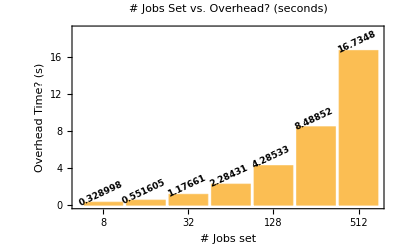

```mathematica
overhead = BarChart[ilaboverhead,ChartLabels->ilabjobString,LabelingFunction->(Placed[Rotate[Style[#1,9,Bold],25 Degree],Above]&),Frame->True,FrameLabel->{"# Jobs set","Overhead Time? (s)"},PlotLabel->"# Jobs Set vs. Overhead? (seconds)",PlotRange->{All,{0,19}}]
```

```mathematica
sidebyside=BarChart[ilabtime,ChartLabels->{ilabjobString,{"expected","meas."}},LabelingFunction->(Placed[Rotate[Style[#1,9,Bold],25 Degree],Above]&),Frame->True,FrameLabel->{"# Jobs set","Time (s)"},PlotLabel->"# Jobs Set vs. Time (seconds)",PlotRange->{All,{0,20500}}]
```

```mathematica
Roverhead=Rasterize[overhead,ImageResolution->200]
Rsidebyside=Rasterize[sidebyside,ImageResolution->500]
```

#### Linear Fit

```mathematica
lm = LinearModelFit[avgPoints,x,x];
Normal[lm]
```

```mathematica
Normal[lm]
```

86.0805-10.4321 x

```mathematica
standardError[ts_]:=StandardDeviation[ts]/Abs[ts]
```

```mathematica
stderr=standardError[avgPoints[[All,2]]]
stderr=Table[{avgPoints[[i,1]],avgPoints[[i,2]],stderr[[i]]},{i,1,3}]
```

{0.211747,0.242451,0.360908}

{{1,75.2895,0.211747},{2,65.7549,0.242451},{4,44.1728,0.360908}}

```mathematica
points=ListPlot[avgPoints,PlotRange->{{0,5},All},PlotMarkers->{Automatic,Small},PlotStyle->{Black,Opacity[0.5]}];

fit=Plot[lm[x],{x,0,5},PlotStyle->{Gray,Dashed},PlotLegends->{"Linear Fit\n"<>ToString[Normal[lm]], FontSize->12}];

Needs["ErrorBarPlots`"]
errplot=ErrorListPlot[stderr,PlotMarkers->{".",Tiny},PlotStyle->{Blue}];

final=Show[{fit,errplot(*,points*)},Frame->True,FrameLabel->{"# cores set","Time (s)"},LabelStyle->Bold,PlotLabel->"# Cores vs. Average MonteCarlo Runtimes",PlotRange->{All,{40,80}}]
```